```mathematica
a={0};
b={1};
p= {a[[1]],a[[1]]+(b[[1]]-a[[1]])/2};
k=1;
F[x_]:=x-2^(-x);
While[(Abs[p[[k+1]]-p[[k]]]>10^(-5)),
k+=1; 
If[F[p[[k]]]!=0,
If[Sign[F[p[[k]]]]==-1,
a=Append[a,p[[k]]];b=Append[b,b[[-1]]];,b=Append[b,p[[k]]];a=Append[a,a[[-1]]]
],Break;
];
p= Append[p,a[[-1]]+(b[[-1]]-a[[-1]])/2];]

m=Table[N[{n,a[[n]],b[[n]],p[[n]],F[p[[n+1]]],Abs[(p[[n+1]]-p[[n]])/p[[n+1]]]},5],{n,1,Length[a]}];
Grid[Prepend[m,{"n","a","b","p","f(p)","ϵ_a"}],Frame->All]
```

n | a | b | p | f(p) | ϵ_a
1. | 0 | 1. | 0 | -0.20711 | 1.
2. | 0.5 | 1. | 0.5 | 0.1554 | 0.33333
3. | 0.5 | 0.75 | 0.75 | -0.02342 | 0.2
4. | 0.625 | 0.75 | 0.625 | 0.066571 | 0.090909
5. | 0.625 | 0.6875 | 0.6875 | 0.021725 | 0.047619
6. | 0.625 | 0.65625 | 0.65625 | -0.00081001 | 0.02439
7. | 0.64063 | 0.65625 | 0.64063 | 0.010467 | 0.012048
8. | 0.64063 | 0.64844 | 0.64844 | 0.0048306 | 0.0060606
9. | 0.64063 | 0.64453 | 0.64453 | 0.0020109 | 0.0030395
10. | 0.64063 | 0.64258 | 0.64258 | 0.0006006 | 0.0015221
11. | 0.64063 | 0.6416 | 0.6416 | -0.00010467 | 0.00076161
12. | 0.64111 | 0.6416 | 0.64111 | 0.00024797 | 0.00038066
13. | 0.64111 | 0.64136 | 0.64136 | 0.000071654 | 0.00019037
14. | 0.64111 | 0.64124 | 0.64124 | -0.000016507 | 0.000095193
15. | 0.64117 | 0.64124 | 0.64117 | 0.000027573 | 0.000047594
16. | 0.64117 | 0.6412 | 0.6412 | 5.5332×10^-6 | 0.000023798
17. | 0.64117 | 0.64119 | 0.64119 | -5.487×10^-6 | 0.000011899

```mathematica
a={1};
b={2};
p= {a[[1]],a[[1]]+(b[[1]]-a[[1]])/2};
k=1;
F[x_]:=x^2-3;
While[(Abs[p[[k+1]]-p[[k]]]>10^(-4)),
k+=1; 
If[F[p[[k]]]!=0,
If[Sign[F[p[[k]]]]==-1,
a=Append[a,p[[k]]];b=Append[b,b[[-1]]];,b=Append[b,p[[k]]];a=Append[a,a[[-1]]]
],Break;
];
p= Append[p,a[[-1]]+(b[[-1]]-a[[-1]])/2];]

m=Table[N[{n,a[[n]],b[[n]],p[[n]],F[p[[n+1]]],Abs[(p[[n+1]]-p[[n]])/p[[n+1]]]},7],{n,1,Length[a]}];
Grid[Prepend[m,{"n","a","b","p","f(p)","ϵ_a"}],Frame->All]
```

n | a | b | p | f(p) | ϵ_a
1. | 1. | 2. | 1. | -0.75 | 0.3333333
2. | 1.5 | 2. | 1.5 | 0.0625 | 0.1428571
3. | 1.5 | 1.75 | 1.75 | -0.359375 | 0.07692308
4. | 1.625 | 1.75 | 1.625 | -0.1523438 | 0.03703704
5. | 1.6875 | 1.75 | 1.6875 | -0.04589844 | 0.01818182
6. | 1.71875 | 1.75 | 1.71875 | 0.008056641 | 0.009009009
7. | 1.71875 | 1.734375 | 1.734375 | -0.01898193 | 0.004524887
8. | 1.726563 | 1.734375 | 1.726563 | -0.005477905 | 0.002257336
9. | 1.730469 | 1.734375 | 1.730469 | 0.001285553 | 0.001127396
10. | 1.730469 | 1.732422 | 1.732422 | -0.00209713 | 0.0005640158
11. | 1.731445 | 1.732422 | 1.731445 | -0.0004060268 | 0.0002819284
12. | 1.731934 | 1.732422 | 1.731934 | 0.0004397035 | 0.0001409443
13. | 1.731934 | 1.732178 | 1.732178 | 0.00001682341 | 0.00007047713
14. | 1.731934 | 1.732056 | 1.732056 | -0.0001946054 | 0.00003523981

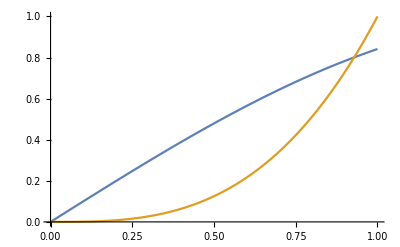

```mathematica
Plot[{Sin[x],x^3},{x,0,1}]
```

```mathematica
a={0.8};
b={1};
p= {a[[1]],a[[1]]+(b[[1]]-a[[1]])/2};
k=1;
F[x_]:=Sin[x]-x^3;
While[(Abs[(p[[k+1]]-p[[k]])/p[[k+1]]]>0.02),
k+=1; 
If[F[p[[k]]]!=0,
If[Sign[F[p[[k]]]]==-1,
a=Append[a,p[[k]]];b=Append[b,b[[-1]]];,b=Append[b,p[[k]]];a=Append[a,a[[-1]]]
],Break;
];
p= Append[p,a[[-1]]+(b[[-1]]-a[[-1]])/2];]

m=Table[N[{n,a[[n]],b[[n]],p[[n]],F[p[[n+1]]],Abs[(p[[n+1]]-p[[n]])/p[[n+1]]]},7],{n,1,Length[a]}];
Grid[Prepend[m,{"n","a","b","p","f(p)","ϵ_a"}],Frame->All]
```

n | a | b | p | f(p) | ϵ_a
1. | 0.8 | 1. | 0.8 | 0.0543269 | 0.111111
2. | 0.8 | 0.9 | 0.9 | 0.137155 | 0.0588235
3. | 0.8 | 0.85 | 0.85 | 0.173032 | 0.030303
4. | 0.8 | 0.825 | 0.825 | 0.189632 | 0.0153846

```mathematica
a1=0;
a2=1;
a={a1};
b={a2};
p= {0,1};
k=2;
F[x_]:=230x^4+18x^3+9x^2-221x-9;
While[(Abs[(p[[k]]-p[[k-1]])/p[[k]]]>10^(-6)),
p= Append[p,a2-(F[a2](a2-a1))/(F[a2]-F[a1])];
k+=1;
If[F[p[[k]]]!=0,
If[Sign[F[p[[k]]]]==Sign[F[a2]],
a2=p[[k]];
,
a1=p[[k]];
],Break;
];
a=Append[a,a1];
b=Append[b,a2];
 ]

m=Table[N[{n,a[[n]],b[[n]],p[[n]],F[p[[n+1]]],Abs[(p[[n+1]]-p[[n]])/p[[n+1]]]},5],{n,1,Length[a]}];
Grid[Prepend[m,{"n","a","b","p","f(p)","ϵ_a"}],Frame->All]
```

n | a | b | p | f(p) | ϵ_a
1. | 0 | 1. | 0 | 27. | 1.
2. | 0.25 | 1. | 1. | -62.508 | 3.
3. | 0.77376 | 1. | 0.25 | -83.831 | 0.6769
4. | 0.94489 | 1. | 0.77376 | -11.265 | 0.1811
5. | 0.96111 | 1. | 0.94489 | -0.85587 | 0.016882
6. | 0.96231 | 1. | 0.96111 | -0.061802 | 0.0012417
7. | 0.96239 | 1. | 0.96231 | -0.0044462 | 0.000089448
8. | 0.9624 | 1. | 0.96239 | -0.00031978 | 6.434×10^-6
9. | 0.9624 | 1. | 0.9624 | -0.000022999 | 4.6274×10^-7

```mathematica
a1=1;
a2=2;
a={a1};
b={a2};
p= {a1,a2};
k=2;
F[x_]:=2x^3-2.5x-5;
While[(Abs[(p[[k]]-p[[k-1]])/p[[k]]]>10^(-6)),
p= Append[p,a2-(F[a2](a2-a1)/2)/(F[a2]/2-F[a1])];
k+=1;
If[F[p[[k]]]!=0,
If[Sign[F[p[[k]]]]==Sign[F[a2]],
a2=p[[k]];
,
a1=p[[k]];
],Break;
];
a=Append[a,a1];
b=Append[b,a2];
 ]

m=Table[N[{n,a[[n]],b[[n]],p[[n+2]],F[p[[n+2]]],Abs[(p[[n+2]]-p[[n+1]])/p[[n+2]]]},5],{n,1,Length[a]-1}];
Grid[Prepend[m,{"n","a","b","p","f(p)","ϵ_a"}],Frame->All]
```

n | a | b | p | f(p) | ϵ_a
1. | 1. | 2. | 1.64706 | -0.181356 | 0.214286
2. | 1.64706 | 2. | 1.66718 | 0.0998462 | 0.0120681
3. | 1.64706 | 1.66718 | 1.66284 | 0.0384648 | 0.00261179
4. | 1.64706 | 1.66284 | 1.66132 | 0.0171739 | 0.000910523
5. | 1.64706 | 1.66132 | 1.66068 | 0.00811146 | 0.000388305
6. | 1.64706 | 1.66068 | 1.66038 | 0.00392758 | 0.000179422
7. | 1.64706 | 1.66038 | 1.66024 | 0.00192407 | 0.0000859533
8. | 1.64706 | 1.66024 | 1.66017 | 0.000947902 | 0.0000418869
9. | 1.64706 | 1.66017 | 1.66013 | 0.000468277 | 0.0000205824
10. | 1.64706 | 1.66013 | 1.66012 | 0.00023165 | 0.000010155
11. | 1.64706 | 1.66012 | 1.66011 | 0.00011467 | 5.02035×10^-6
12. | 1.64706 | 1.66011 | 1.6601 | 0.0000567826 | 2.48438×10^-6
13. | 1.64706 | 1.6601 | 1.6601 | 0.0000281222 | 1.23002×10^-6
14. | 1.64706 | 1.6601 | 1.6601 | 0.000013929 | 6.09137×10^-7